# 5

## PHAS2443: Practical Mathematics II Lecture 5: Classification of Differential Equations and Relaxation Methods

## Classification of differential equations

The first rule of attack should always be 'know thine enemy', and that holds as much for the solution of differential equations as in other walks of life. Here we will discuss how second-order partial differential equations are classified, and what their classification says about the ways we can solve them.

We consider equations of the general form:
  A(ϕ,x,y)(∂^2 ϕ)/(∂x^2)+ B(ϕ,x,y) (∂^2 ϕ)/(∂x∂y) +C(ϕ,x,y) (∂^2 ϕ)/(∂y^2)+D(ϕ,x,y) (∂ϕ)/(∂x)+E(ϕ,x,y) (∂ϕ)/(∂y)+F(ϕ,x,y) ϕ =0,  
  but note that x and y are just labels for two independent variables -- in practice one of these might be a spatial dimension and the other might be time, or they might both be spatial dimensions. Some of the key equations of mathematical physics are:
   One-dimensional wave equation:
   (∂^2 ϕ)/(∂x^2)-1/c^2 (∂^2 ϕ)/(∂t^2)= 0.
      Multi-dimensional wave equation:
   ∇^2 ϕ-1/c^2 (∂^2 ϕ)/(∂t^2)= 0.
      Laplace's equation:
   ∇^2 ϕ =(∂^2 ϕ)/(∂x^2)+(∂^2 ϕ)/(∂y^2)+(∂^2 ϕ)/(∂z^2)= 0.
      Diffusion/Heat equation:
      ∇^2 ϕ-1/κ (∂ϕ)/(∂t)= 0.
      Schrodinger equation:
      -ℏ^2/(2m)∇^2 ϕ + V ϕ = ⅈℏ(∂ϕ)/(∂t),
      or, in a stationary state,
      -ℏ^2/(2m)∇^2 ϕ + (V-E) ϕ = 0.
      All these equations are linear second-order equations. They are also homogeneous. This means that if ϕ is a solution, so is any constant multiple of ϕ. In many problems we need to consider inhomogeneous problems, in which there is a forcing term -- for example, in the heat equation there might be a source of heat so that
      ∇^2 ϕ-1/K (∂ϕ)/(∂t)-1/κ Q(x,t)= 0,
   Note that there are two different constants, the thermal diffusivity K=κ/cρ, and the thermal conductivity κ.
   
   Any differential equation requires boundary conditions. If we are solving the equation in some region Ω of the (x,y)-plane, surrounded by a boundary Γ, we can imagine three ways of specifying the boundary conditions: these are named after famous characters in the history of differential equations:
    a) Dirichlet conditions: ϕ is specified at each point on the boundary,
    b) Neumann conditions: ∇_n ϕ, the component of the gradient of ϕ normal to the boundary,is specified at each point on the boundary,
    c) Cauchy conditions: ϕ and ∇_n ϕ are specified at each point on the boundary.
    
    
   If we think back to ordinary differential equations, we might expect that Cauchy conditions on a line would be a natural set of boundary conditions. After all, in one dimension knowing ϕ and ϕ' was enough to find ϕ'', and then to start off a Taylor series expansion. In two (and more) dimensions life is a bit more complicated.
   
   Suppose that the boundary Γ is specified parametrically in terms of s, a length along the boundary: 
                           x=x(s),   y=y(s),
  and suppose that we are told ϕ(s) and the normal derivative on the boundary, N(s). The unit normal to the boundary is n=(-dy/ds,dx/ds), so that
      N(s) = n.∇ϕ=∇_n ϕ = - (∂ϕ)/(∂x) dy/ds + (∂ϕ)/(∂y) dx/ds
which we can put together with the derivative of ϕ along the boundary
  d/ds ϕ = (∂ϕ)/(∂x) dx/ds + (∂ϕ)/(∂y) dy/ds
and solved for the first derivatives of ϕ, remembering we chose unit normal so that (dx/ds)^2+(dy/ds)^2=1:
 (∂ϕ)/(∂x)= -N(s) dy/ds+(dϕ(s))/ds dx/ds
 and
 (∂ϕ)/(∂y)= N(s) dx/ds+(dϕ(s))/ds dy/ds.
 When we come to the second derivatives, we can get two equations by differentiating those we have just found:
 d/ds (∂ϕ)/(∂x)= (∂^2 ϕ)/(∂x^2) dx/ds + (∂^2 ϕ)/(∂x∂y) dy/ds
d/ds (∂ϕ)/(∂y)= (∂^2 ϕ)/(∂x∂y) dx/ds + (∂^2 ϕ)/(∂y^2) dy/ds
and the third equation is the original differential equation, If we write this in the form:
A(∂^2 ϕ)/(∂x^2)+ B (∂^2 ϕ)/(∂x∂y) + C(∂^2 ϕ)/(∂y^2)= f,
where f  is a known function of x, y, ϕ, and the first derivatives, we can solve for the three second derivatives (∂^2 ϕ/∂x^2,∂^2 ϕ/∂x∂y,∂^2 ϕ/∂y^2) unless the determinant of the 3×3 linear system of equation vanishes, that is, unless
det(dx/ds | dy/ds | 0
0 | dx/ds | dy/ds
A | B | C)=0
or
(A(dy/ds))^2 - B dx/ds dy/ds + C (dx/ds)^2=0.
At each point in the plane, this equation defines two directions, dx/ds and dy/ds, which are called the characteristic directions at that point. We can draw curves in the plane which are everywhere tangential to the characteristic directions, and these are called the characteristic curves of the partial differential equation. As long as the boundary Γ is nowhere tangential to a characterstic curve, we can start our solution off in the same way as for a one dimensional equation, with Cauchy boundary conditions. Note that although we called the independent variables x and y, they could equally well have been, for example, x and t.

   Note that in general the coefficents A, B, C, D, E, and F, as well as G, may be functions of ϕ, x and y. Equations are classified according to the values of the discriminant function Δ=B^2-4 A C:
    If Δ >0, the equation is called hyperbolic: in this case the characteristics are real curves,
    if Δ =0, the equation is called parabolic,
    if Δ < 0, the equation is called elliptic.
    
    To go further one needs to analyse the way in which the characteristic curves divide space into regions, and deduce from that the boundary conditions that are required to establish a solution. For the wave equation, A=1, B=0 and C=-1/c^2, thus  the discriminant Δ > 0, and the family of characteristic curves is particularly simple: (dy/ds-1/c dx/ds) (dy/ds+1/c dx/ds)=0

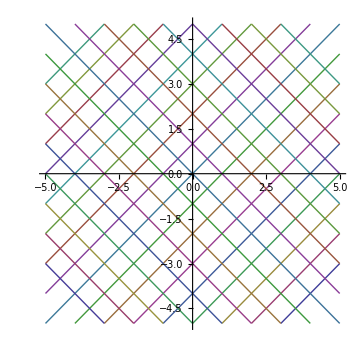

```mathematica
pc=Plot[Evaluate[Flatten[{Table[x+i,{i,-8,8}],Table[-x+i,{i,-8,8}]}]],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->Automatic]
```

In fact, if we think of the vertical axis as time and the horizontal as position, these lines just represent rays travelling in the positive or negative x direction at the speed of the wave.  Now suppose we specify Cauchy boundary conditions on a line that is not part of a characteristic -- for example, the line AB in space at time zero.

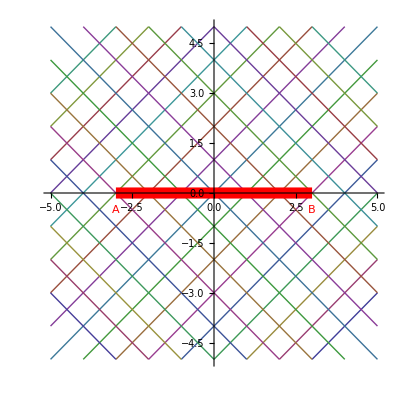

```mathematica
pl=Graphics[{Thickness[.02],RGBColor[1,0,0],Line[{{-3,0},{3,0}}],Text["A",{-3,-.5}],Text["B",{3,-.5}]}];
Show[pc,pl]
```

then this will define the solution over any region that cannot be influenced by information from outside that line -- given that the information propagates at the wave speed, as shown by the characteristics, this means that we can find the solution over the region:

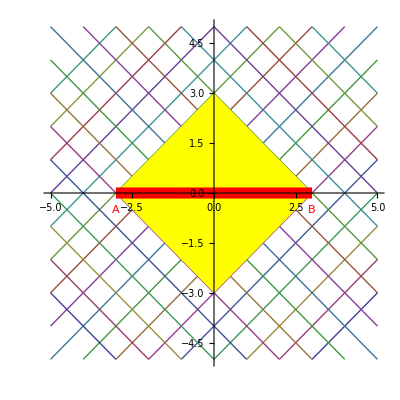

```mathematica
sh=Graphics[{RGBColor[1,1,0],Polygon[{{-3,0},{0,3},{3,0},{0,-3}}]}];
Show[pc,sh,pl]
```

Note that the boundary does not (indeed, in general, should not) enclose the area of interest for a hyperbolic equation. For an elliptic equation, the situation is quite different. Here we must specify a closed boundary -- there are no real characteristics, and information diffuses in from the boundary rather than propagating along characteristics. We can summarise the types of boundary equation that apply to the different types of equation as follows:

Equation | Condition | Boundary
Hyperbolic | Cauchy | Open
Elliptic | Dirichlet or Neumann | Closed
Parabolic | Dirichlet or Neuman | Open

### Example and a Caution

We can classify the diffusion equation (or heat equation) 
 (∂θ)/(∂t)= 1/K (∂^2 θ)/(∂x^2) 
 in which there is only one second-order derivative by identifying A=1/K, B=0 and C=0, so the discriminant Δ=0, thus the equation is parabolic. 
 
 Note that one cannot just say 'oh, a heat problem -- that will be parabolic.'  Suppose we look at the steady-state distribution of temperature in two dimensions. Without going through the formal derivation, it is fairly easy to see what the equation must be. If the temperature is not varying with time, it means there must be no net heat flow into or out of any volume. This means that the divergence of the heat flux must be zero (remember Gauss's theorem which links flux through a closed surface with divergence). But the heat flux is proportional to the temperature gradient. So we have (assuming the thermal conductivity κ is constant, that is, does not depend on temperature, position or time),
   div grad θ  =  0
   or
   ∇.∇θ = 0
   which, in a more explicit form, is in 2D:
   (∂^2 θ)/(∂x^2)+ (∂^2 θ)/(∂y^2)= 0.
 Now, of course, A=C=1 and B=0, so we have an elliptic equation. As the nature of the equation (in terms of its classification as elliptic, parabolic or hyperbolic) does not change if we add a term corresponding to G in the original equation we could add a source of heat, itself a function of position (but not time) into the problem. If the source provides energy input Q(x,y) per unit time and the thermal conductivity is κ, the equation becomes
   (∂^2 θ)/(∂x^2)+ (∂^2 θ)/(∂y^2)= -1/κQ,
 and is still elliptic. 
  Another important elliptic equation is Poisson's equation, which relates electrostatic potential to charge density. Poisson's equation is just the inhomogeneous form of Laplace's equation.

The wave equation is an important example of a hyperbolic equation, in:
(∂^2 θ)/(∂t^2) -c^2 (∂^2 θ)/(∂x^2)=0,
 we may identify A=1, B=0 and C=-c^2, so that the discriminant Δ is positive and the system is hyperbolic.
 
   We have explored some solution methods for parabolic equations already, in our modelling of heat flow -- although at the time we had not introduced this classification scheme. In the remainder of this lecture we shall talk about some schemes for elliptic problems, and in the next lecture we will tackle a hyperbolic system, the wave equation.

## Methods for Elliptic problems

If we consider Laplace's equation in two dimensions:
(∂^2 ϕ)/(∂x^2)+(∂^2 ϕ)/(∂y^2)= 0,
the physical problem we solve may correspond to the steady-state distribution of temperature in an insulated plate, or the electrostatic potential in a two-dimensional region. As noted above, this is an elliptic equation. If we apply a simple finite difference scheme, with meshes Δx and Δy in the two spatial dimensions. We get
(ϕ_(i+1,j)-2 ϕ_(i,j)+ϕ_(i-1,j))/Δx^2+(ϕ_(i,j+1)-2 ϕ_(i,j)+ϕ_(i,j-1))/Δy^2 = 0. 
For simplicity, assume that Δx = Δy, then:
ϕ_(i+1,j)+ϕ_(i-1,j)+ϕ_(i,j+1)+ϕ_(i,j-1)-4 ϕ_(i,j)=0. 
Consider now a specific small problem: a square with left and right edges held at ϕ=300, top and bottom edges at ϕ=400. Set up a coarse mesh:

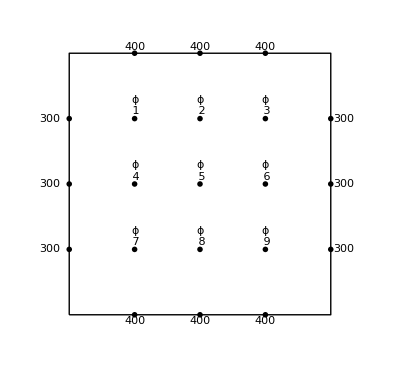

```mathematica
Show[Graphics[Flatten[{PointSize[0.01],Line[{{-2,-2},{2,-2},{2,2},{-2,2},{-2,-2}}],
Table[{Text["400",{i,2.1}],Point[{i,2}]},{i,-1,1}],
Table[{Text["400",{i,-2.1}],Point[{i,-2}]},{i,-1,1}],
Table[{Text["300",{-2.3,j}],Point[{-2,j}]},{j,-1,1}],
Table[{Text["300",{2.2,j}],Point[{2,j}]},{j,-1,1}],Table[{Text[ToString[Subscript[ϕ, 2+3(-j+1)+i]],{i,j+.2}],Point[{i,j}]},{i,-1,1},{j,-1,1}]}]],AspectRatio->Automatic,PlotRange->{{-2.5,2.5},{-2.3,2.3}}]
```

Formally, we can see that we can write the difference equations as a set of simultaneous equations (note that because our difference scheme only involves points separated vertically or horizontally, and not diagonally, we do not have to face up to the question of what temperatures to apply as a boundary condition in the corners):
  ϕ_2 + 300 + 400 + ϕ_4-4 ϕ_1=0
  ϕ_3 + ϕ_1 + 400 + ϕ_5 - 4 ϕ_2 = 0
  300 + ϕ_2 + 400 + ϕ_6 - 4 ϕ_3 = 0
  ϕ_5 + 300 + ϕ_1 + ϕ_7-4 ϕ_4=0
  ϕ_6 + ϕ_4 + ϕ_2 + ϕ_8 - 4 ϕ_5 = 0
  300 + ϕ_5 + ϕ_3 + ϕ_9 - 4 ϕ_6 = 0
  ϕ_8 + 300 + ϕ_4 + 400-4 ϕ_7=0
   ϕ_9 + ϕ_7 + ϕ_5 + 400 - 4 ϕ_8 = 0
  300 + ϕ_8 + ϕ_6 + 400 - 4 ϕ_9 = 0.
  With 9 unknowns and 9 equations, we can obviously solve this set of linear equations.

### Matrix Methods

There are several approaches to this solution process. The direct approach would be to rewrite the equations in matrix form:
      M ϕ = b
  where
     M = (-4 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | -4 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | -4 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | -4 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | -4 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | -4 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | -4 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | -4 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -4),
     Note that this is not our old friend the tridiagonal matrix. The bandwidth (amount of the matrix occupied on each side of the diagonal) is greater than three, and there are some zero entries within the tridiagonal band. In general, in a two-dimensional problem such as this, the bandwidth gets greater as the mesh gets bigger (but if the array of points is not square, we can make the bandwidth narrower by being careful about the way we lable the points). ϕ is the vector of unknown temperatures
      ϕ^T=(ϕ_1,ϕ_2,ϕ_3,ϕ_4,ϕ_5,ϕ_6,ϕ_7,ϕ_8,ϕ_9)
      and b represents the boundary conditions, which inspection of the set of simultaneous equations shows can be written as
      ϕ^T= (-700,-400,-700,-300,0,-300,-700,-400,-700).
      Simple matrix solution then gives

{350.,362.5,350.,337.5,350.,337.5,350.,362.5,350.}

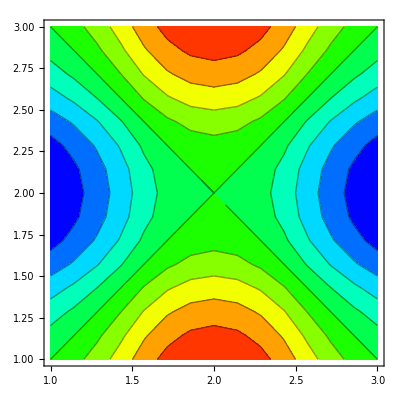

```mathematica
mmat= ({{-4, 1, 0, 1, 0, 0, 0, 0, 0}, {1, -4, 1, 0, 1, 0, 0, 0, 0}, {0, 1, -4, 0, 0, 1, 0, 0, 0}, {1, 0, 0, -4, 1, 0, 1, 0, 0}, {0, 1, 0, 1, -4, 1, 0, 1, 0}, {0, 0, 1, 0, 1, -4, 0, 0, 1}, {0, 0, 0, 1, 0, 0, -4, 1, 0}, {0, 0, 0, 0, 1, 0, 1, -4, 1}, {0, 0, 0, 0, 0, 1, 0, 1, -4}});
b={-700,-400,-700,-300,0,-300,-700,-400,-700};
ϕ=MatrixPower[mmat,-1].b//N
ListContourPlot[Partition[ϕ,3],DataRange->All,ColorFunction->(Hue[.7(1-#)]&),InterpolationOrder->2]
```

(As an aside: Hue is a nice way of applying a colour that is just determined by the value of a function: the only problem is that both the minimum and maximim values of Hue (0 and 1) correspond to red:

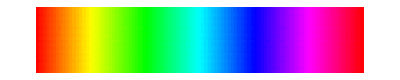

```mathematica
ListDensityPlot[Table[i/200,{j,0,10},{i,1,100}],AspectRatio->Automatic,ColorFunction->Hue,Mesh->False,Frame->False,PlotRegion->{{0,1},{0,.5}}]
```

whereas a more intuitive scaling has a 'cold to hot' colour mapping)

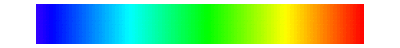

```mathematica
ListDensityPlot[Table[i/200,{j,0,10},{i,1,100}],AspectRatio->.1,ColorFunction->(Hue[.7(1-#)]&),Mesh->False,Frame->False,PlotRegion->{{0,1},{0,.5}}]
```

## Relaxation Methods

As matrices get big, inverting them gets expensive. It is worth looking at an older way of tackling problems of this kind. Mathematically, these approaches, called relaxation methods, work because the matrices involved are diagonally dominant, that is,
   M_ii > ∑_(j≠i)^N|M_ij|.

### Gauss-Seidel Method

The first approach is called the Gauss-Seidel method. In this approach the set of simultaneous equations is rewritten so that the terms with the largest coefficients are rewritten in terms of the neighbouring points, i.e.:
    ϕ_1=1/4( ϕ_2 +ϕ_4+700)
    ϕ_2 = 1/4(ϕ_1 + ϕ_3  + ϕ_5+ 400)
   ϕ_3 = 1/4(ϕ_2 + ϕ_6 + 700)
   ϕ_4=1/4(ϕ_1 +ϕ_5+ϕ_7+300)
   ϕ_5 = 1/4(ϕ_2 + ϕ_4 + ϕ_6 + ϕ_8 )
    ϕ_6 = 1/4( ϕ_3 + ϕ_5 + ϕ_9+300)
   ϕ_7=1/4(ϕ_4 + ϕ_8 + 700)
    ϕ_8 =1/4(ϕ_5 + ϕ_7 + ϕ_9 + 400 )
  ϕ_9 =1/4(ϕ_6 + ϕ_8 + 700 )
  The procedure is as follows:
    a) estimate the temperature at each point (for example, starting with the average of the boundary temperatures)
    b) use the first equation to make a new estimate of ϕ_1
    c) use this estimate in the second equation to get a new estimate of ϕ_2
    d) continue through all the equations.
    e) if there have been significant changes, start again with the current estimates of ϕ.
    Here is a Mathematica form of the algorithm:

```mathematica
Clear[ϕ]
eq[1]:=ϕ[[1]]=(ϕ[[2]]+ϕ[[4]]+700)/4
eq[2]:=ϕ[[2]]=(ϕ[[1]]+ϕ[[3]]+ϕ[[5]]+400)/4
eq[3]:=ϕ[[3]]=(ϕ[[2]]+ϕ[[6]]+700)/4
eq[4]:=ϕ[[4]]=(ϕ[[1]]+ϕ[[5]]+ϕ[[7]]+300)/4
eq[5]:=ϕ[[5]]=(ϕ[[2]]+ϕ[[4]]+ϕ[[6]]+ϕ[[8]])/4
eq[6]:=ϕ[[6]]=(ϕ[[3]]+ϕ[[5]]+ϕ[[9]]+300)/4
eq[7]:=ϕ[[7]]=(ϕ[[4]]+ϕ[[8]]+700)/4
eq[8]:=ϕ[[8]]=(ϕ[[5]]+ϕ[[7]]+ϕ[[9]]+400)/4
eq[9]:=ϕ[[9]]=(ϕ[[6]]+ϕ[[8]]+700)/4
ϕ=Table[350.,{i,1,9}];
ϕt={ϕ};
Do[Do[eq[j],{j,1,9}];AppendTo[ϕt,ϕ],{6}]
TableForm[ϕt]
```

350. | 350. | 350. | 350. | 350. | 350. | 350. | 350. | 350.
350. | 362.5 | 353.125 | 337.5 | 350. | 338.281 | 346.875 | 361.719 | 350.
350. | 363.281 | 350.391 | 336.719 | 350. | 337.598 | 349.609 | 362.402 | 350.
350. | 362.598 | 350.049 | 337.402 | 350. | 337.512 | 349.951 | 362.488 | 350.
350. | 362.512 | 350.006 | 337.488 | 350. | 337.502 | 349.994 | 362.498 | 350.
350. | 362.502 | 350.001 | 337.498 | 350. | 337.5 | 349.999 | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.

As we can see, the process converges quite rapidly. Even if we make a very poor starting guess, it still works.

```mathematica
ϕ=Table[1000.,{i,1,9}];
ϕt2={ϕ};
Do[Do[eq[j],{j,1,9}];AppendTo[ϕt2,ϕ],{23}]
TableForm[ϕt2]
```

1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000.
675. | 768.75 | 617.188 | 743.75 | 878.125 | 698.828 | 610.938 | 722.266 | 530.273
553.125 | 612.109 | 502.734 | 585.547 | 654.688 | 496.924 | 501.953 | 521.729 | 429.663
474.414 | 507.959 | 426.221 | 482.764 | 502.344 | 414.557 | 426.123 | 439.532 | 388.522
422.681 | 437.811 | 388.092 | 412.787 | 426.172 | 375.697 | 388.08 | 400.694 | 369.098
387.65 | 400.478 | 369.044 | 375.475 | 388.086 | 356.557 | 369.042 | 381.556 | 359.528
368.988 | 381.53 | 359.522 | 356.529 | 369.043 | 347.023 | 359.521 | 372.023 | 354.762
359.515 | 372.02 | 354.761 | 347.02 | 359.521 | 342.261 | 354.761 | 367.261 | 352.38
354.76 | 367.261 | 352.38 | 342.261 | 354.761 | 339.88 | 352.38 | 364.88 | 351.19
352.38 | 364.88 | 351.19 | 339.88 | 352.38 | 338.69 | 351.19 | 363.69 | 350.595
351.19 | 363.69 | 350.595 | 338.69 | 351.19 | 338.095 | 350.595 | 363.095 | 350.298
350.595 | 363.095 | 350.298 | 338.095 | 350.595 | 337.798 | 350.298 | 362.798 | 350.149
350.298 | 362.798 | 350.149 | 337.798 | 350.298 | 337.649 | 350.149 | 362.649 | 350.074
350.149 | 362.649 | 350.074 | 337.649 | 350.149 | 337.574 | 350.074 | 362.574 | 350.037
350.074 | 362.574 | 350.037 | 337.574 | 350.074 | 337.537 | 350.037 | 362.537 | 350.019
350.037 | 362.537 | 350.019 | 337.537 | 350.037 | 337.519 | 350.019 | 362.519 | 350.009
350.019 | 362.519 | 350.009 | 337.519 | 350.019 | 337.509 | 350.009 | 362.509 | 350.005
350.009 | 362.509 | 350.005 | 337.509 | 350.009 | 337.505 | 350.005 | 362.505 | 350.002
350.005 | 362.505 | 350.002 | 337.505 | 350.005 | 337.502 | 350.002 | 362.502 | 350.001
350.002 | 362.502 | 350.001 | 337.502 | 350.002 | 337.501 | 350.001 | 362.501 | 350.001
350.001 | 362.501 | 350.001 | 337.501 | 350.001 | 337.501 | 350.001 | 362.501 | 350.
350.001 | 362.501 | 350. | 337.501 | 350.001 | 337.5 | 350. | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.

### Over-Relaxation Methods

What we can see, looking at the columns (or, more clearly, by plotting the temperatures at each point as a function of iteration number)

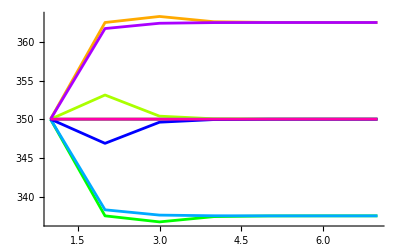

```mathematica
ListPlot[Transpose[ϕt],Joined->True,PlotStyle->Table[{Thickness[0.005],Hue[x]},{x,0,1,1./Length[Transpose[ϕt]]}]]
```

that after some initial large changes the temperatures seem to converge monotonically on the final solution. This suggests a method (called, for historical reasons, over-relaxation) in which the change made at each step is increased slightly. The factor by which it is increased is known as the over-relaxation factor. Here is an example, with the over-relaxation factor w set to 1.05:

```mathematica
w=1.05;
eq[1]:=ϕ[[1]]=ϕ[[1]]+w(ϕ[[2]]+ϕ[[4]]+700-4ϕ[[1]])/4
eq[2]:=ϕ[[2]]=ϕ[[2]]+w(ϕ[[1]]+ϕ[[3]]+ϕ[[5]]+400-4ϕ[[2]])/4
eq[3]:=ϕ[[3]]=ϕ[[3]]+w(ϕ[[2]]+ϕ[[6]]+700-4ϕ[[3]])/4
eq[4]:=ϕ[[4]]=ϕ[[4]]+w(ϕ[[1]]+ϕ[[5]]+ϕ[[7]]+300-4ϕ[[4]])/4
eq[5]:=ϕ[[5]]=ϕ[[5]]+w(ϕ[[2]]+ϕ[[4]]+ϕ[[6]]+ϕ[[8]]-4ϕ[[5]])/4
eq[6]:=ϕ[[6]]=ϕ[[6]]+w(ϕ[[3]]+ϕ[[5]]+ϕ[[9]]+300-4ϕ[[6]])/4
eq[7]:=ϕ[[7]]=ϕ[[7]]+w(ϕ[[4]]+ϕ[[8]]+700-4ϕ[[7]])/4
eq[8]:=ϕ[[8]]=ϕ[[8]]+w(ϕ[[5]]+ϕ[[7]]+ϕ[[9]]+400-4ϕ[[8]])/4
eq[9]:=ϕ[[9]]=ϕ[[9]]+w(ϕ[[6]]+ϕ[[8]]+700-4ϕ[[9]])/4
ϕ=Table[1000.,{i,1,9}];
ϕt={ϕ};
Do[Do[eq[j],{j,1,9}];AppendTo[ϕt,ϕ],{20}]
TableForm[ϕt]
```

1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000.
658.75 | 752.922 | 593.892 | 726.672 | 863.393 | 673.787 | 587.001 | 698.229 | 493.904
539.206 | 591.433 | 486.176 | 564.687 | 620.466 | 465.204 | 485.915 | 490.163 | 409.839
460.271 | 486.743 | 409.327 | 461.762 | 468.743 | 393.566 | 409.335 | 418.57 | 376.444
409.719 | 418.708 | 376.505 | 393.709 | 403.008 | 362.51 | 376.506 | 387.51 | 361.808
376.523 | 387.524 | 361.809 | 362.524 | 373.618 | 348.649 | 361.809 | 373.649 | 355.263
361.812 | 373.649 | 355.263 | 348.649 | 360.525 | 342.468 | 355.263 | 367.468 | 352.345
355.263 | 367.468 | 352.345 | 342.468 | 354.69 | 339.714 | 352.345 | 364.714 | 351.045
352.345 | 364.714 | 351.045 | 339.714 | 352.09 | 338.487 | 351.045 | 363.487 | 350.466
351.045 | 363.487 | 350.466 | 338.487 | 350.932 | 337.94 | 350.466 | 362.94 | 350.208
350.466 | 362.94 | 350.208 | 337.94 | 350.415 | 337.696 | 350.208 | 362.696 | 350.092
350.208 | 362.696 | 350.092 | 337.696 | 350.185 | 337.587 | 350.092 | 362.587 | 350.041
350.092 | 362.587 | 350.041 | 337.587 | 350.082 | 337.539 | 350.041 | 362.539 | 350.018
350.041 | 362.539 | 350.018 | 337.539 | 350.037 | 337.517 | 350.018 | 362.517 | 350.008
350.018 | 362.517 | 350.008 | 337.517 | 350.016 | 337.508 | 350.008 | 362.508 | 350.004
350.008 | 362.508 | 350.004 | 337.508 | 350.007 | 337.503 | 350.004 | 362.503 | 350.002
350.004 | 362.503 | 350.002 | 337.503 | 350.003 | 337.502 | 350.002 | 362.502 | 350.001
350.002 | 362.502 | 350.001 | 337.502 | 350.001 | 337.501 | 350.001 | 362.501 | 350.
350.001 | 362.501 | 350. | 337.501 | 350.001 | 337.5 | 350. | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.

As we can see, this has speeded up the convergence significantly. The result may be that by using over-relaxation we use fewer arithmetic operations than would have been needed for a matrix solution, and thus the solution might be faster.

  The question then is, how should one choose the over-relaxation factor? To find the optimal value requires some matrix algebra, but one can show that for Laplace's equation (which we have just been solving) set up with N cells of size Δx along the x axis and M cells of size Δy along the y axis the best over-relaxation factor is
    w=2/(1+√(1-ξ)),
    where
    	ξ={(cos(π/N) + (Δx/Δy)^2 cos(π/M))/(1+ (Δx/Δy)^2)}^2.
    	Notice that the optimal factor depends on the size of the problem. For the example we have been using, Δx=Δy and N=M=5, (if we include the points in the boundary in the count -- of course, for our ridiculously small mesh the difference between N and N+2 matters, but for a large mesh it will be irrelevant) so

```mathematica
ξ=((cos(π/N) + (Δx/Δy)^2 cos(π/M))/(1+ (Δx/Δy)^2))^2/.{Δx->Δy,N->5,M->5}
w=2/(1+√(1-ξ))//N
```

1/16 (1+√5)^2

1.25962

This suggests that our previous guess at an over-relaxation factor was a bit too small. If we try again with this value we find the following.

```mathematica
ϕ=Table[1000.,{i,1,9}];
ϕt={ϕ};
Do[Do[eq[j],{j,1,9}];AppendTo[ϕt,ϕ],{13}]
TableForm[ϕt]
```

1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000. | 1000.
590.625 | 682.144 | 490.53 | 650.653 | 789.895 | 552.97 | 480.614 | 581.338 | 318.015
486.8 | 505.373 | 426.36 | 478.935 | 462.091 | 330.832 | 429.542 | 355.96 | 354.145
404.014 | 401.761 | 340.44 | 378.136 | 341.9 | 334.975 | 340.087 | 359.831 | 347.288
361.137 | 350.253 | 347.83 | 324.785 | 342.606 | 334.29 | 347.729 | 359.296 | 348.684
339.248 | 359.282 | 348.539 | 334.372 | 347.901 | 336.798 | 348.595 | 361.814 | 349.905
350.793 | 362.464 | 350.147 | 337.459 | 350.084 | 337.725 | 350.136 | 362.717 | 350.164
349.77 | 362.509 | 350.036 | 337.507 | 350.123 | 337.543 | 350.035 | 362.545 | 349.985
350.065 | 362.568 | 350.026 | 337.568 | 350.039 | 337.504 | 350.027 | 362.504 | 350.007
350.026 | 362.511 | 349.998 | 337.511 | 350. | 337.5 | 349.998 | 362.5 | 349.998
350. | 362.497 | 349.999 | 337.496 | 349.998 | 337.499 | 349.999 | 362.499 | 350.
349.998 | 362.499 | 350. | 337.499 | 349.999 | 337.5 | 350. | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.
350. | 362.5 | 350. | 337.5 | 350. | 337.5 | 350. | 362.5 | 350.

### Computational Complexity

This is far from the end of the story : two other approaches to the solution of elliptic problems exist, called cyclic reduction and multigrid methods. It is interesting to see how the computational complexity of the solutions has reduced over time, as a function of the size of the problem, N.

Method | Date | Complexity
Matrix solution (Gaussian elimination) | 1945 | N^7
Successive overrelaxation (Suboptimal) | 1954 | 8 N^5
Successive overrelaxation (Optimal) | 1960 | 8 N^4 log_2 N
Cyclic reduction | 1970 | 8 N^3 log_2 N
Multigrid | 1978 | 60 N^3

## Summary

The important point that comes out of today's work is that the sort of boundary conditions that have to be specified differ for different classes of differential equation. We have now looked at solution methods for parabolic and elliptic equations. In the next lecture we will tackle hyperbolic equations -- the classical wave equation and Schrodinger's equation.

A.H. Harker
Physics and Astronomy, UCL
September 2005, revised January 2009, December 2010.
Amended by Patrick Guio, Physics and Astronomy, UCL, February 2014-2017.